```mathematica
AppendTo[$Path,"C:\\Users\\hp\\Desktop\\Wolfram Summer School\\project\\Tile\\GeneralTile"];
Get["happytile.wl"]
```

## Inner vertices?

```mathematica
spectreInnerVertices[pos_,dir_,ref_,pt_]:=Expand[
(If[TrueQ[ref],{-#[[1]],#[[2]]},#]&/@ (.Transpose@RotationMatrix[dir Pi/6]))+Threaded[spectreVertices[pos,dir,ref,pt][[1]]]
]
```

```mathematica
divideSpectre[pos_,dir_,ref_,pt_]:=With[{
vs=spectreVertices[pos,dir,ref,pt],
ivs=spectreInnerVertices[pos,dir,ref,pt]
},
{
{vs[[8]],ivs[[1]]},
ivs,
{ivs[[2]],vs[[13]]}
}
]
```

## Mystery Triple

```mathematica
makeMystery[pos_,dir_:0,pt_:1]:=canonicalTile[{1,1}]@@@NestList[{(spectreVertices@@#)[[9]],Mod[#[[2]]+1,12],False,1}&,{pos,dir,False,pt},2];
```

```mathematica
mystery=NestList[{(spectreVertices@@#)[[9]],Mod[#[[2]]+1,12],False,1}&,{{0,0},0,False,1},2];
```

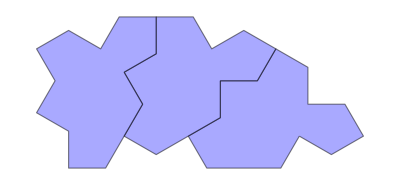

```mathematica
show[mystery,step->{1,1}]
```

## Sample clusters

0-super-tile

```mathematica
cluster=;
```

1-super-tile

```mathematica
supertile1=;
```

## A quick depict function

```mathematica
quickDepictDivision[code_]:=Graphics[
{
EdgeForm[Black],
Opacity[.8],
{
{Lighter@Red,Polygon[shape1[##]]}&@@@#1,
{Lighter@Blue,Polygon[shape2[##]]}&@@@#2
}&@@Transpose[spectreCodeToShapes@@@code]
}
]
```

## Split a Spectre into two?

```mathematica
shape1[or_,dir_,pt_]:=With[{
basicVertices = AnglePath[{
 -Pi/6+dir*Pi/6,Pi/3, Pi/2,
Pi/3,-Pi/2,Pi/3,Pi/2,
Pi/3,-Pi/2,Pi/3,Pi/2
}]
},
	Expand[(( basicVertices - Threaded[basicVertices[[pt]]] )  + Threaded[or])]
]
```

```mathematica
shape2[or_,dir_,pt_]:=With[{basicVertices = AnglePath[{ -Pi/6+dir*Pi/6,Pi/2,Pi/3,Pi/2,-Pi/3,Pi/2,Pi/3,Pi/2}]},
Expand[(( basicVertices - Threaded[basicVertices[[pt]]] )  + Threaded[or])]
]
```

```mathematica
spectreCodeToShapes[or_,dir_,ref_,pt_]:=With[{
vs=spectreVertices[or,dir,ref,pt],
ivs=spectreInnerVertices[or,dir,ref,pt]
},
{
{vs[[1]],If[TrueQ[ref],Mod[-dir-1,12],dir],1},
{ivs[[2]],If[TrueQ[ref],Mod[-dir-2,12],dir+2],1}
}
]
```

```mathematica
Show[
Polygon/@({shape1@@#1,shape2@@#2}&@@spectreCodeToShapes[{0,-10},2,True,2])//Graphics[{Opacity[.5],#}]&
,show[{{{0,-10},2,True,2}},step->{1,1}],
Graphics[{Red,Disk[spectreInnerVertices[{0,-10},2,True,2],.1]}]
]
```

-Graphics-

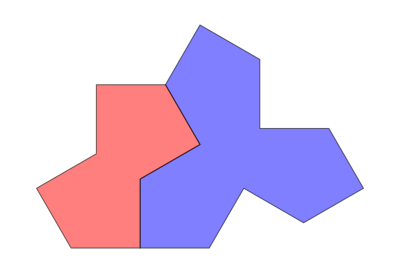

```mathematica
Graphics[{
EdgeForm[Black],
Opacity[.5],
Blue,
Polygon[shape1[{0,0},0,1]],
Red,
Polygon[shape2[shape1[{0,0},0,1][[10]],2,1]]
}]
```

## Split Examples

### 1/3 1/4 v.f.

```mathematica
codes=Map[Prepend[#,{0,0}]&,Join@@(#[{1,1}]&/@{oneThirdVertexTheoremLis,TshapeList,oneFourthVertexTheoremLis}),{2}];
```

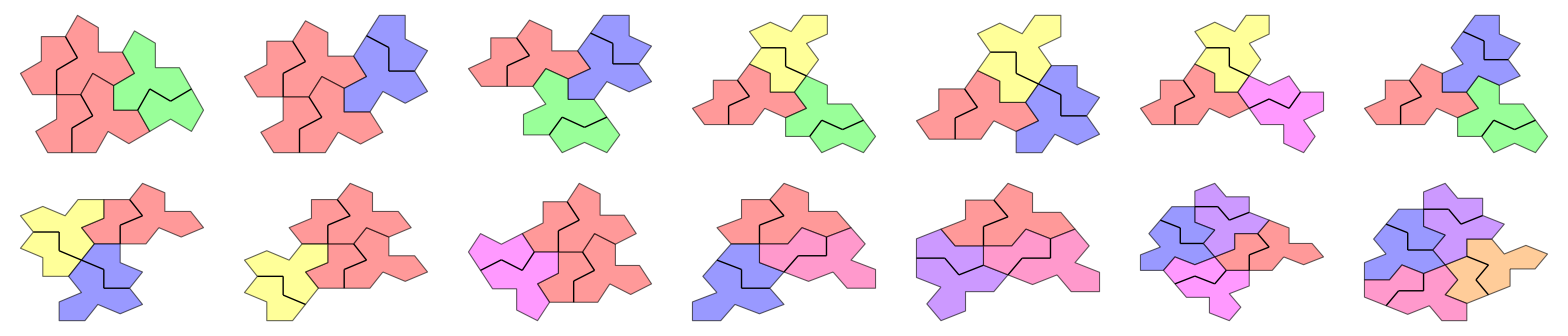

```mathematica
Show[
Graphics[
{
EdgeForm[Directive[Black,Thick]],
Opacity[.6],
Replace[#,{{pos_,dir_,ref_,pt_}:>{Lighter@Hue[dir/12],spectre[pos,dir,ref,pt]}},{1}]
}
],
Graphics[{Thick,Black,Line/@(Join@@(divideSpectre@@@#))}]
]&/@codes//Partition[#,UpTo[7]]&//Grid
```

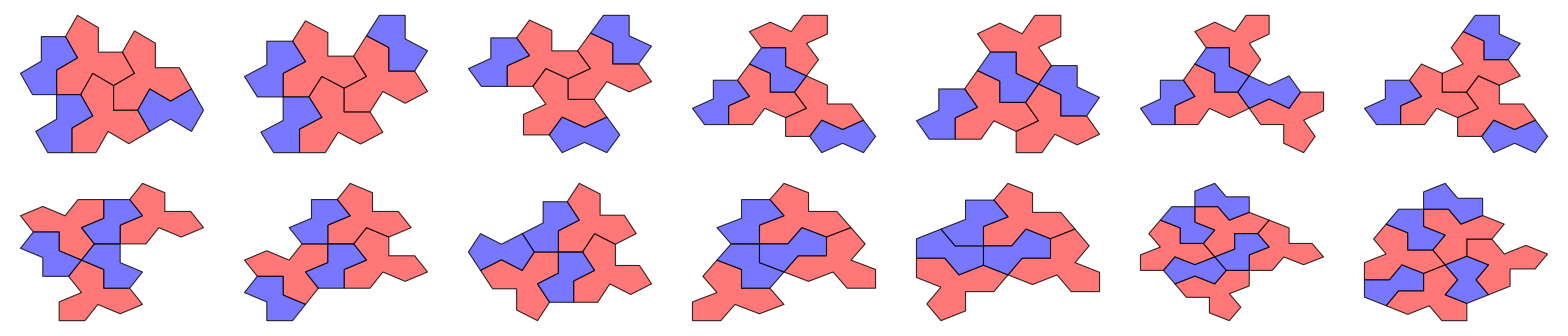

```mathematica
Graphics[
{
EdgeForm[Black],
Opacity[.8],
{
{Lighter@Red,Polygon[shape1[##]]}&@@@#1,
{Lighter@Blue,Polygon[shape2[##]]}&@@@#2
}&@@Transpose[spectreCodeToShapes@@@#]
}
]&/@codes//Partition[#,UpTo[7]]&//Grid
```

### 0-super-tile

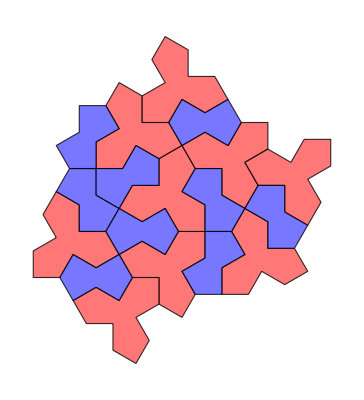
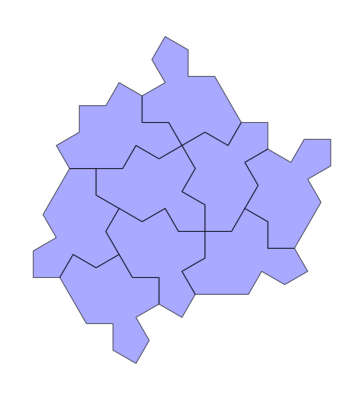

```mathematica
#@cluster&/@{quickDepictDivision,show[#,step->{1,1}]&}
```

Meta-tiles:

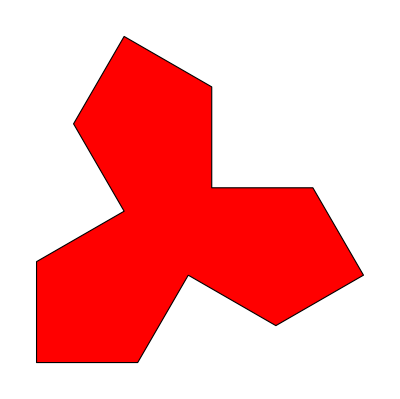
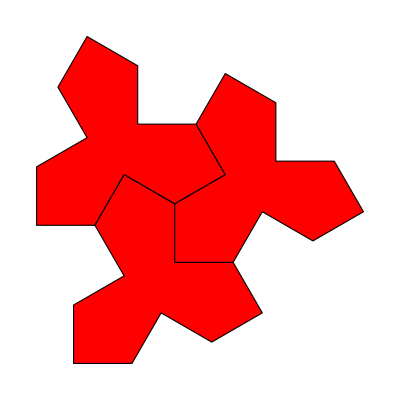
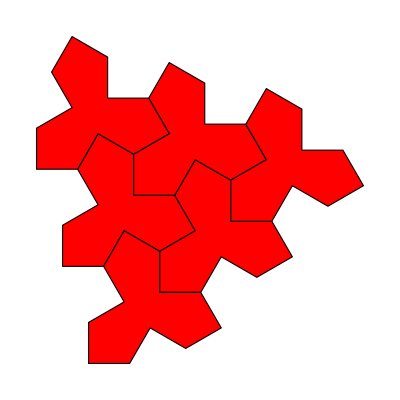

```mathematica
{
Graphics[
{
EdgeForm[Black],
Red,
Polygon[shape1[##]]&@@@{{{0,0},0,1}}
}],
Graphics[
{
EdgeForm[Black],
Red,
Polygon[shape1[##]]&@@@{{{0,0},0,2},{{0,0},0,6},{{0,0},0,10}}
}],
Graphics[
{
EdgeForm[Black],
Red,
Polygon[shape1[##]]&@@@{
{{0,0},0,4},{{0,0},0,8},{{0,0},0,12},
{shape1[{0,0},0,4][[6]],0,2},{shape1[{0,0},0,4][[2]],0,6},{shape1[{0,0},0,8][[6]],0,10}
}
}]
}//Row
```

Polygon union:

```mathematica
T[class_][pos_,dir_,pt_]:=With[{
vs=Switch[class,1,,2,,3,].Transpose[RotationMatrix[dir*Pi/6]]
},
vs+Threaded[pos-vs[[pt]]]
]
```

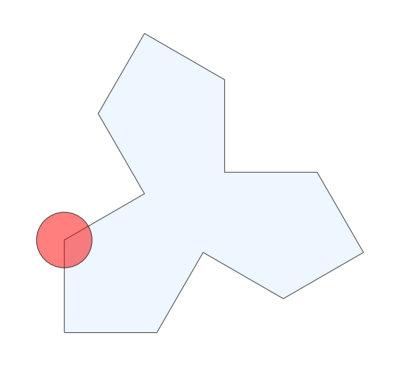
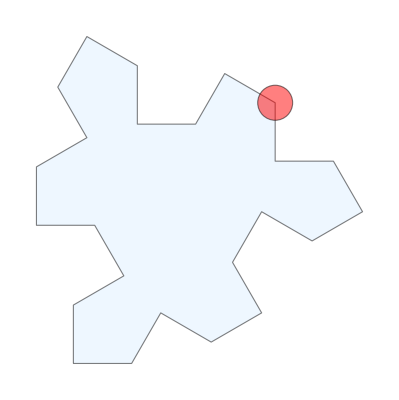
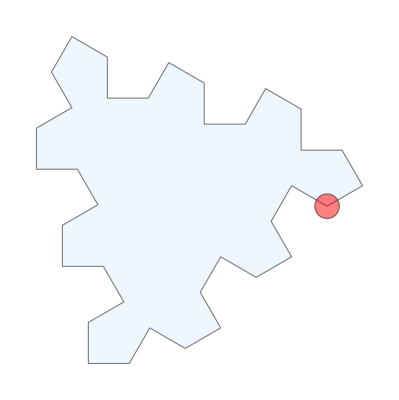

```mathematica
Graphics[{LightBlue,EdgeForm[Black],Opacity[.5],Polygon[T[#][{0,0},0,12]],Red,Disk[{0,0},.3]}]&/@{1,2,3}
```

## Big data

```mathematica
data=;
```

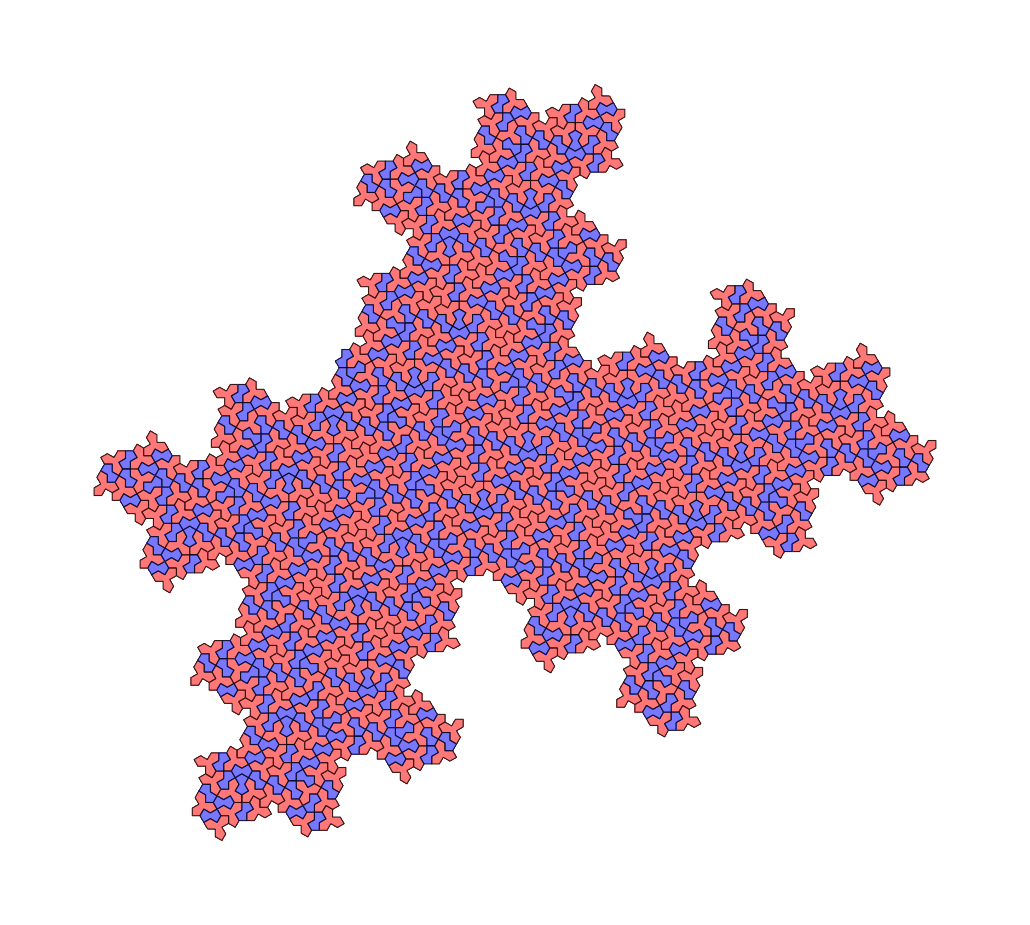

```mathematica
Show[#,ImageSize->900]&[quickDepictDivision@data[[2]]]
```

It looks like both blue and red tiles only have three kinds of meta cluster respectively?